# Figure 9

#### Data

```mathematica
datfid={{0,0.9630808397122281},{5,0.9664787548149494},{10,0.9687051015874895},{15,0.9722947013892114},{20,0.9764256579395322},{25,0.9809026941616624},{30,0.9853218419851063},{35,0.9893476203658351},{40,0.9927522726016893},{45,0.9954272555293262},{50,0.9973559857387267},{55,0.9986516180545215},{60,0.9994379250832992},{65,1.0000520678040352},{70,1.0002464708629506},{75,1.0003388345579691},{80,1.0004062244141958}};
datneg={{0,0},{5,0.0034014594915687812},{10,0.0034591270101649307},{15,0.003890222152318046},{20,0.00610873028435055},{25,0.012657986652043318},{30,0.024141961611362284},{35,0.037975782770635735},{40,0.05127430325385274},{45,0.06189173629320743},{50,0.0687905669878559},{55,0.07210464930602645},{60,0.0725801863970108},{65,0.07186747405650729},{70,0.07123475982151639},{75,0.07280785920519528},{80,0.07803435697853578}};
datfidn=Table[{datfid[[i,1]],datfid[[i,2]]-0.0004},{i,1,Length[datfid]}];
datfid2={{0,0.057634071870660226},{5,0.07576209201225834},{10,0.17747007172053086},{15,0.3841891338915353},{20,0.6151878840035238},{25,0.7199286466241821},{30,0.7243998075423707},{35,0.7496145766226694},{40,0.7950261049064292},{45,0.8184064911740184},{50,0.8239640459263688},{55,0.8343741472496772},{60,0.8500654371823333},{65,0.8597280108952984},{70,0.8638033672951273},{75,0.8689911628442414},{80,0.8756531937674544}};
datneg2={{0,0},{5,0.0025258388199835835},{10,0.016660295453891916},{15,0.12223186616452097},{20,0.19205754510578132},{25,0.14620277556716466},{30,0.14200412759555636},{35,0.25641947510439045},{40,0.35754791075982384},{45,0.39462776380995046},{50,0.44037594802703817},{55,0.5498045381068384},{60,0.6593438742227029},{65,0.724753788235958},{70,0.796797218257963},{75,0.9073517474084731},{80,1.0196787386276673}};
datfidn2=Table[{datfid2[[i,1]],datfid2[[i,2]]-0.0004},{i,1,Length[datfid2]}];
```

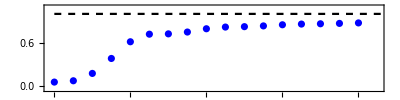

```mathematica
fig8a = Show[ListPlot[{datfidn2}, Joined -> False,
   PlotStyle -> {Blue, Thickness[0.0043]}, 
   PlotRange -> {{-1,85},{-0.05,1.1}}, 
   GridLines -> {{}, {}}, GridLinesStyle -> {{}, {}}, 
   Frame -> True, LabelStyle -> {10, Black}],Plot[1,{x,0,1100},PlotStyle->{Black,Dashed}], AspectRatio -> 0.25]
```

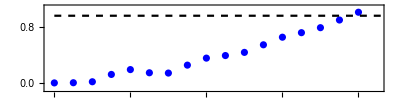

```mathematica
fig8b= Show[ListPlot[{datneg2}, Joined -> False,
   PlotStyle -> {Blue, Thickness[0.0043]}, 
   PlotRange -> {{-1,85},{-0.1,1.1}}, 
   GridLines -> {{}, {}}, GridLinesStyle -> {{Red,Dashed}, {}},Axes->False, 
   Frame -> True, LabelStyle -> {10, Black}],Plot[{0.9691},{x,0,1100},PlotStyle->{{Black,Dashed}}], AspectRatio -> 0.25]
```